### Definitions

```mathematica
(*Define particle Number Np, number of dimensions d, modes m natural length scales in terms of kappa (=k) as well as coordinates*)
Np=5;
d = 1;
lm = 1;
lp[k_]:=((k+1)^(1/4))/lm;
$Assumptions = -1<k && Im[k]==0
xcoord={x1,x2,x3, x4,x5}
xpcoord = {x1p,x2p,x3p, x4p,x5p}
```

-1<k&&Im[k]==0

{x1,x2,x3,x4,x5}

{x1p,x2p,x3p,x4p,x5p}

```mathematica
(*Define A, Subscript[B, N] and the natural length in terms of l_+=lp and l_-=s*)
A[lp_]:=1/(2 lp^2);
B[lm_,lp_, Np_]:=-1/(2Np) (1/lm^2-1/lp^2);
l[lm_,lp_, Np_]:=1/((((Np-1) lm^2+lp^2)/(lm^4 lp^2+(Np-1) lm^2 lp^4))^(1/4))
f[a_,b_,Np_] := ((Np-2)*b^2/2)/(a-(Np-2)b)-((Np-1)*b^2/2)/(a-(Np-1)b);
```

### Defining Exponential Functions, Normalization and HF Basis Functions

```mathematica
(*efunN denote the exponential functions for the N-particle reduced densitry operator and efun..poly defines the polynomial of the exponential*)
```

```mathematica
efun5[a_,b_, x1_, x2_, x3_, x4_,x5_]:=Exp[-a(x1^2+x2^2+x3^2+x4^2+x5^2)+b(x1+x2+x3+x4+x5)^2];
efun5poly[a_,b_, x1_, x2_, x3_, x4_,x5_]:=-a(x1^2+x2^2+x3^2+x4^2+x5^2)+b(x1+x2+x3+x4+x5)^2
```

```mathematica
efun4[a_,b_,x1_,x2_,x3_,x4_,x1p_,x2p_,x3p_,x4p_]:=ⅇ^(-(b^2 (x1-x1p+x2-x2p+x3-x3p+x4-x4p)^2+2 a^2 (x1^2+x1p^2+x2^2+x2p^2+x3^2+x3p^2+x4^2+x4p^2)-4 a b (x1^2+x1p^2+x2^2+x2p^2+x2 x3+x3^2+x2p x3p+x3p^2+x2 x4+x3 x4+x4^2+x1 (x2+x3+x4)+x2p x4p+x3p x4p+x4p^2+x1p (x2p+x3p+x4p)))/(2 (a-b)))
```

```mathematica
efun4poly[a_,b_]:=-1/(2 (a-b))(b^2 (x1-x1p+x2-x2p+x3-x3p+x4-x4p)^2+2 a^2 (x1^2+x1p^2+x2^2+x2p^2+x3^2+x3p^2+x4^2+x4p^2)-4 a b (x1^2+x1p^2+x2^2+x2p^2+x2 x3+x3^2+x2p x3p+x3p^2+x2 x4+x3 x4+x4^2+x1 (x2+x3+x4)+x2p x4p+x3p x4p+x4p^2+x1p (x2p+x3p+x4p)))
```

```mathematica
efun3[a_,b_, x1_, x2_, x3_, x1p_, x2p_, x3p_]:=ⅇ^(-(b^2 (x1-x1p+x2-x2p+x3-x3p)^2+a^2 (x1^2+x1p^2+x2^2+x2p^2+x3^2+x3p^2)-a b (3 x1^2+3 x1p^2+3 x2^2+3 x2p^2+2 x2 x3+3 x3^2+2 x1 (x2+x3)+2 x2p x3p+3 x3p^2+2 x1p (x2p+x3p)))/(a-2 b))
```

```mathematica
efun3poly[a_,b_]:=-1/(a-2 b)(b^2 (x1-x1p+x2-x2p+x3-x3p)^2+a^2 (x1^2+x1p^2+x2^2+x2p^2+x3^2+x3p^2)-a b (3 x1^2+3 x1p^2+3 x2^2+3 x2p^2+2 x2 x3+3 x3^2+2 x1 (x2+x3)+2 x2p x3p+3 x3p^2+2 x1p (x2p+x3p)));
cp[a_,b_,Np_]:=((Np-2)*b^2/2)/(a-(Np-2)*b);
efunana2rdo[a_,b_,Np_, x1_, x1p_, x2_, x2p_]:=Exp[-a(x1^2+x2^2+x1p^2+x2p^2)+b((x1+x2)^2+(x1p+x2p)^2)+cp[a,b,Np]*(x1+x1p+x2+x2p)^2];
```

```mathematica
efun2poly[a_,b_, Np_,x1_,x2_,x1p_,x2p_]:=-a(x1^2+x2^2+x1p^2+x2p^2)+b((x1+x2)^2+(x1p+x2p)^2)+cp[a,b,Np]*(x1+x1p+x2+x2p)^2;


efun1[a_,b_, x1_, x1p_]:=Exp[-(a-b-b^2(Np-1)/(2(a-b(Np-1))))(x1^2+x1p^2)]*Exp[b^2(Np-1)/(a-b(Np-1)) x1* x1p];
efun1poly[a_,b_]:=-(a-b-b^2(Np-1)/(2(a-b(Np-1))))(x1^2+x1p^2)+(b^2(Np-1)/(a-b(Np-1)) x1* x1p)
```

```mathematica
(*norm /normpre denotes the normalization of the N-particle RDO with respect to the intrinisc length scales lm, lp or the constants A/B*)
```

```mathematica
norm5rdopre[a_,b_, Np_]:=(π^(5/2)/(4 √2 a^2 √(a-5 b)))^(-1);
norm5rdo[lm_,lp_, Np_]:=norm5rdopre[A[lp],B[lm,lp, Np], Np];
norm4rdopre[a_,b_, Np_]:=((√((a-b)/(a-5 b)) π^2)/(4 a^2))^(-1);
norm4rdo[lm_,lp_, Np_]:=norm4rdopre[A[lp],B[lm,lp, Np], Np];
```

```mathematica
norm3rdopre[a_,b_, Np_]:=((√((a-2 b)/(a^3 (a-5 b))) π^(3/2))/(2 √2))^(-1);
norm3rdo[lm_,lp_, Np_]:=norm3rdopre[A[lp],B[lm,lp, Np], Np];
norm2rdopre[a_,b_, Np_]:=(π/(2 √((a (a-5 b))/(a-4 b)) √((a (a-4 b))/(a-3 b))))^(-1);
norm2rdo[lm_,lp_, Np_]:=norm2rdopre[A[lp],B[lm,lp, Np], Np];
norm1rdopre[a_,b_, Np_]:=(√((a-4 b)/(a^2-5 a b)) √(π/2))^(-1)
norm1rdo[lm_,lp_, Np_]:=norm1rdopre[A[lp],B[lm,lp, Np], Np];
```

```mathematica
(*define 2 particle hf basis in terms of permanents*)
hfcoef[n_,x_, a_]:=(Factorial[n]2^n π^(1/2)  )^(-1/2)*(2*a)^(1/4)* HermiteH[n,(x*Sqrt[2a])]
hf2basis[m1_, m2_, n1_,n2_,a_]:=1/2(hfcoef[m1,x1,a]*hfcoef[m2,x2, a]+hfcoef[m2,x1,a]*hfcoef[m1,x2,a])*1/2(hfcoef[n1,x1p,a]*hfcoef[n2,x2p,a]+hfcoef[n2,x1p,a]*hfcoef[n1,x2p,a])
hf3basis[m1_, m2_,m3_, n1_,n2_,n3_,a_]:=1/6*Permanent[{{hfcoef[m1,x1,a], hfcoef[m1,x2,a], hfcoef[m1,x3,a]},{hfcoef[m2,x1,a], hfcoef[m2,x2,a], hfcoef[m2,x3,a]},{hfcoef[m3,x1,a], hfcoef[m3,x2,a], hfcoef[m3,x3,a]}}]*1/6*Permanent[{{hfcoef[n1,x1p,a], hfcoef[m1,x2p,a], hfcoef[m1,x3p,a]},{hfcoef[m2,x1p,a], hfcoef[m2,x2p,a], hfcoef[m2,x3p,a]},{hfcoef[m3,x1p,a], hfcoef[m3,x2p,a], hfcoef[m3,x3p,a]}}]
hf4basis[m1_, m2_,m3_,m4_, n1_,n2_,n3_,n4_,a_]:=1/24*Permanent[{{hfcoef[m1,x1,a], hfcoef[m1,x2,a], hfcoef[m1,x3,a], hfcoef[m1, x4,a]},{hfcoef[m2,x1,a], hfcoef[m2,x2,a], hfcoef[m2,x3,a], hfcoef[m2,x4,a]},{hfcoef[m3,x1,a], hfcoef[m3,x2,a], hfcoef[m3,x3,a], hfcoef[m3,x4,a]},{hfcoef[m4,x1,a], hfcoef[m4,x2,a], hfcoef[m4,x3,a], hfcoef[m4,x4,a]}}]*1/24*Permanent[{{hfcoef[m1,x1p,a], hfcoef[m1,x2p,a], hfcoef[m1,x3p,a], hfcoef[m1, x4p,a]},{hfcoef[m2,x1p,a], hfcoef[m2,x2p,a], hfcoef[m2,x3p,a], hfcoef[m2,x4p,a]},{hfcoef[m3,x1p,a], hfcoef[m3,x2p,a], hfcoef[m3,x3p,a], hfcoef[m3,x4p,a]},{hfcoef[m4,x1p,a], hfcoef[m4,x2p,a], hfcoef[m4,x3p,a], hfcoef[m4,x4p,a]}}]
hf1basis[m1_, n1_,a_]:=(hfcoef[m1,x1,a]*hfcoef[n1,x1p,a])
hf5basis[m1_, m2_,m3_,m4_,m5_, n1_,n2_,n3_,n4_,n5_,a_]:=1/120*Permanent[{{hfcoef[m1,x1,a], hfcoef[m1,x2,a], hfcoef[m1,x3,a], hfcoef[m1, x4,a],  hfcoef[m1, x5,a]},{hfcoef[m2,x1,a], hfcoef[m2,x2,a], hfcoef[m2,x3,a], hfcoef[m2,x4,a],  hfcoef[m2, x5,a]},{hfcoef[m3,x1,a], hfcoef[m3,x2,a], hfcoef[m3,x3,a], hfcoef[m3,x4,a],  hfcoef[m3, x5,a]},{hfcoef[m4,x1,a], hfcoef[m4,x2,a], hfcoef[m4,x3,a], hfcoef[m4,x4,a],  hfcoef[m4, x5,a]}, {hfcoef[m5,x1,a], hfcoef[m5,x2,a], hfcoef[m5,x3,a], hfcoef[m5,x4,a],  hfcoef[m5, x5,a]}}]*1/120*Permanent[{{hfcoef[m1,x1p,a], hfcoef[m1,x2p,a], hfcoef[m1,x3p,a], hfcoef[m1, x4p,a], hfcoef[m1, x5p,a]},{hfcoef[m2,x1p,a], hfcoef[m2,x2p,a], hfcoef[m2,x3p,a], hfcoef[m2,x4p,a], hfcoef[m2, x5p,a]},{hfcoef[m3,x1p,a], hfcoef[m3,x2p,a], hfcoef[m3,x3p,a], hfcoef[m3,x4p,a], hfcoef[m3, x5p,a]},{hfcoef[m4,x1p,a], hfcoef[m4,x2p,a], hfcoef[m4,x3p,a], hfcoef[m4,x4p,a], hfcoef[m4, x5p,a]}, {hfcoef[m5,x1p,a], hfcoef[m5,x2p,a], hfcoef[m5,x3p,a], hfcoef[m5,x4p,a], hfcoef[m5, x5p,a]}}]
```

### Determining the coefficients of the Polynomial Contribution to the integral

```mathematica
(*Determine the coefficients of the polynomial 'hfibasis' by the coefficientlist function where q corresponds to the power, i.e. x^q , importantly this is not the mathematica index, maxdegreestart denotes the largest q in the polynomial with non-zero entries*)
```

```mathematica
coefstart5[m1_, m2_,m3_,m4_,m5_, n1_,n2_,n3_,n4_,n5_,x_,q_,a_] :=CoefficientList[hf5basis[m1,m2,m3,m4,m5,n1,n2,n3,n4,n5,a], x][[q+1]]
maxdegreestart5[m1_, m2_,m3_,m4_,m5_, n1_,n2_,n3_,n4_,n5_, x_] := Length[CoefficientList[hf5basis[m1,m2,m3,m4,m5,n1,n2,n3,n4,n5,a], x]]-1
constantstart5[m1_, m2_,m3_,m4_,m5_, n1_,n2_,n3_,n4_,n5_,x_] := coefstart5[m1,m2,m3,m4,m5,n1,n2,n3,n4,n5,x,1,a]
```

```mathematica
coefstart4[m1_, m2_,m3_,m4_, n1_,n2_,n3_,n4_,x_,q_,a_] :=CoefficientList[hf4basis[m1,m2,m3,m4,n1,n2,n3,n4,a], x][[q+1]]
maxdegreestart4[m1_, m2_,m3_,m4_, n1_,n2_,n3_,n4_, x_] := Length[CoefficientList[hf4basis[m1,m2,m3,m4,n1,n2,n3,n4,a], x]]-1
constantstart4[m1_, m2_,m3_,m4_, n1_,n2_,n3_,n4_,x_] := coefstart3[m1,m2,m3,m4,n1,n2,n3,n4,x,1,a]

coefstart3[m1_, m2_,m3_, n1_,n2_,n3_,x_,q_,a_] :=CoefficientList[hf3basis[m1,m2,m3,n1,n2,n3,a], x][[q+1]]
maxdegreestart3[m1_, m2_,m3_, n1_,n2_,n3_, x_] := Length[CoefficientList[hf3basis[m1,m2,m3,n1,n2,n3,a], x]]-1
constantstart3[m1_, m2_,m3_, n1_,n2_,n3_,x_] := coefstart3[m1, m2,m3, n1,n2,n3,x,1,a]

coefstart2[m1_, m2_, n1_,n2_,x_,q_,a_] :=CoefficientList[hf2basis[m1,m2,n1,n2,a], x][[q+1]]
maxdegreestart2[m1_,m2_,n1_,n2_, x_] := Length[CoefficientList[hf2basis[m1,m2,n1,n2,a], x]]-1
constantstart2[m1_, m2_, n1_,n2_,x_] := coefstart2[m1, m2, n1,n2,x,1,a]

coefstart1[m1_, n1_,x_,q_,a_] :=CoefficientList[hf1basis[m1,n1,a], x][[q+1]]
maxdegreestart1[m1_,n1_, x_] := Length[CoefficientList[hf1basis[m1,n1,a], x]]-1
constantstart1[m1_, n1_,x_] := coefstart1[m1, n1,x,1,a]
```

```mathematica
coefstart2[2,2,2,2,x1,1,a]
```

0

```mathematica
Sum[coefstart3[5,5,2,5,4,3,x1,q,a]*x1^q,{q,0,maxdegreestart3[5,5,2,5,4,3,x1]}]-hf3basis[5,5,2,5,4,3,a]//Simplify
```

0

### Integrating coefficient by coefficient and determining helper functions/exponential polynomials

```mathematica
polycoef[poly_, x_,q_]:= CoefficientList[poly, x][[q+1]]
maxdegreepoly[poly_, x_]:=Length[CoefficientList[poly, x]]-1
```

```mathematica
(*exppolyinitN is the polynomial of the Exp contribution to the N-particle RDO*)
```

```mathematica
exppolyinit5 = efun5poly[a,b,x1,x2,x3, x4,x5]+efun5poly[a,b,x1p,x2p,x3p, x4p,x5p]-a(x1^2+x2^2+x3^2+x4^2+x5^2+x1p^2+x2p^2+x3p^2+x4p^2+x5p^2)
exppolyinit4 = efun4poly[a,b]-a(x1^2+x2^2+x3^2+x4^2+x1p^2+x2p^2+x3p^2+x4p^2)
exppolyinit3 = efun3poly[a,b]-a(x1^2+x2^2+x3^2+x1p^2+x2p^2+x3p^2);
exppolyinit2=-2a*(x1^2+x2^2+x1p^2+x2p^2)+b((x1+x2)^2+(x1p+x2p)^2)+cp[a,b,Np]*(x1+x1p+x2+x2p)^2;
```

b (x1+x2+x3+x4+x5)^2-a (x1^2+x2^2+x3^2+x4^2+x5^2)+b (x1p+x2p+x3p+x4p+x5p)^2-a (x1p^2+x2p^2+x3p^2+x4p^2+x5p^2)-a (x1^2+x1p^2+x2^2+x2p^2+x3^2+x3p^2+x4^2+x4p^2+x5^2+x5p^2)

-a (x1^2+x1p^2+x2^2+x2p^2+x3^2+x3p^2+x4^2+x4p^2)-1/(2 (a-b))(b^2 (x1-x1p+x2-x2p+x3-x3p+x4-x4p)^2+2 a^2 (x1^2+x1p^2+x2^2+x2p^2+x3^2+x3p^2+x4^2+x4p^2)-4 a b (x1^2+x1p^2+x2^2+x2p^2+x2 x3+x3^2+x2p x3p+x3p^2+x2 x4+x3 x4+x4^2+x1 (x2+x3+x4)+x2p x4p+x3p x4p+x4p^2+x1p (x2p+x3p+x4p)))

```mathematica
exppolyinit1 = efun1poly[a,b]-a(x1^2+x1p^2)
```

(4 b^2 x1 x1p)/(a-4 b)-a (x1^2+x1p^2)+(-a+b+(2 b^2)/(a-4 b)) (x1^2+x1p^2)

```mathematica
efuncoef[exppoly_, x_,q_] :=CoefficientList[exppoly, x][[q+1]];
```

```mathematica
(*sanity check to see whether coefficients have been correctly decomposed*)
exppolyinit3-(Sum[efuncoef[exppolyinit3,x1,q]*x1^q, {q,0,2}])  // Simplify
```

0

```mathematica
(* the intxmab function is the results of the following integral:
 Integrate[x^m* Exp[a x^2+b x],{x,-∞,∞}, Assumptions->a<0 && m∈Integers && Im[b]==0]*, it gives the integral over all space of x^m* Exp[a x^2+b x], where the function inputs correspond to the polynomial power, quadratic and linear exponential coefficient respectively *)
intxmab[m_, a_, b_]:=1/2 (-a)^(-m/2) (1/a(-1+(-1)^m) b Gamma[1+m/2] Hypergeometric1F1[1+m/2,3/2,-b^2/(4 a)]+((1+(-1)^m) Gamma[(1+m)/2] Hypergeometric1F1[(1+m)/2,1/2,-b^2/(4 a)])/(√-a))
(*intxmabpoly returns the polynomial contribution of the integration inxmab*)
intxmabpoly[m_,a_,b_]:=intxmab[m,a,b]*Exp[(b^2)/(4a)]
```

```mathematica
(*intexppoly defines the remaining part of the exponential function which in "Running the algorithm" consists of all the coefficients in the remaining variables*)
```

```mathematica
intexppoly[a_,b_]:=-(b^2)/(4a)
```

```mathematica
(*intNpoly is the initial polynomial used to run the integration algorithm which iteratively applies the intmxab function to all different variables one after the other. x1 has been picked as the first integration variable, intgenpoly takes a subsequently evaluated polynomial poly as input to evaluate the integral with respect to the exppoly expontial and the variable xint*)
int5poly[m1_,m2_,m3_,m4_,m5_,n1_,n2_,n3_,n4_,n5_]:= Sum[coefstart5[m1,m2,m3,m4,m5,n1,n2,n3,n4,n5,x1, q, a ]*intxmabpoly[q,efuncoef[exppolyinit5, x1, 2], efuncoef[exppolyinit5, x1, 1]], {q,0, maxdegreestart5[m1,m2,m3,m4,m5,n1,n2,n3,n4, n5,x1]}]
int4poly[m1_,m2_,m3_,m4_,n1_,n2_,n3_,n4_]:= Sum[coefstart4[m1,m2,m3,m4,n1,n2,n3,n4,x1, q, a ]*intxmabpoly[q,efuncoef[exppolyinit4, x1, 2], efuncoef[exppolyinit4, x1, 1]], {q,0, maxdegreestart4[m1,m2,m3,m4,n1,n2,n3,n4, x1]}]
int3poly[m1_,m2_,m3_,n1_,n2_,n3_]:= Sum[coefstart3[m1,m2,m3,n1,n2,n3,x1, q, a ]*intxmabpoly[q,efuncoef[exppolyinit3, x1, 2], efuncoef[exppolyinit3, x1, 1]], {q,0, maxdegreestart3[m1,m2,m3,n1,n2,n3, x1]}]
int2poly[m1_,m2_,n1_,n2_]:= Sum[coefstart2[m1,m2,n1,n2,x1, q, a ]*intxmabpoly[q,efuncoef[exppolyinit2, x1, 2], efuncoef[exppolyinit2, x1, 1]], {q,0, maxdegreestart2[m1,m2,n1,n2, x1]}]
int1poly[m1_,n1_]:= Sum[coefstart1[m1,n1,x1, q, a ]*intxmabpoly[q,efuncoef[exppolyinit1, x1, 2], efuncoef[exppolyinit1, x1, 1]], {q,0, maxdegreestart1[m1,n1, x1]}]
```

```mathematica
intgenpoly[ poly_, exppoly_, xint_]:= Sum[polycoef[poly,xint, q ]*intxmabpoly[q,efuncoef[exppoly, xint, 2], efuncoef[exppoly, xint, 1]], {q,0, maxdegreepoly[poly, xint]}]
```

## Running the algorithm for the various particle sectors

```mathematica
(*pick mode which is used to partition the system*)
```

```mathematica
mode = 2
```

2

```mathematica
(*the algorithm runs recursively,such that polymi and exppolymi (m <-> N=1, mm <-> N=2, mmm <-> N=3, mmmm <-> N=4, mmmmm, <-> N=5) define the relevant polynomials and exponential functions which arise from integrating in the various variables*)
```

### Run algorithm for 1 RDO

```mathematica
polym1 = int1poly[mode, mode];
exppolym1= efuncoef[exppolyinit1, x1, 0]+ intexppoly[efuncoef[exppolyinit1, x1, 2], efuncoef[exppolyinit1, x1, 1]] // Simplify
```

(a (-4 a^2+20 a b-9 b^2) x1p^2)/(2 a^2-9 a b+2 b^2)

```mathematica
polym2 = intgenpoly[polym1, exppolym1, x1p] // Simplify
exppolym2 = efuncoef[exppolym1, x1p, 0]+ intexppoly[efuncoef[exppolym1, x1p, 2], efuncoef[exppolym1, x1p, 1]] // Simplify
```

(√a b^2 (4 a^2-20 a b+57 b^2) √(π/2))/(√((2 a^2-9 a b+2 b^2)/(a-4 b)) (4 a^2-20 a b+9 b^2)^2 √((a (4 a^2-20 a b+9 b^2))/(2 a^2-9 a b+2 b^2)))

0

```mathematica
finalanswerm =norm1rdopre[a,b,Np]* polym2*Exp[exppolym2]
```

(√a b^2 (4 a^2-20 a b+57 b^2))/(√((a-4 b)/(a^2-5 a b)) √((2 a^2-9 a b+2 b^2)/(a-4 b)) (4 a^2-20 a b+9 b^2)^2 √((a (4 a^2-20 a b+9 b^2))/(2 a^2-9 a b+2 b^2)))

### Run algorithm for 2 RDO

```mathematica
polymm1 = int2poly[mode, mode, mode, mode];
```

```mathematica
exppolymm1 = efuncoef[exppolyinit2, x1, 0]+ intexppoly[efuncoef[exppolyinit2, x1, 2], efuncoef[exppolyinit2, x1, 1]] // Simplify;
```

```mathematica
polymm2 = intgenpoly[polymm1, exppolymm1, x2] // Simplify;
```

```mathematica
exppolymm2 = efuncoef[exppolymm1, x2, 0] + intexppoly[efuncoef[exppolymm1, x2, 2], efuncoef[exppolymm1, x2, 1]] // Simplify;
```

```mathematica
polymm3 = intgenpoly[polymm2, exppolymm2, x1p] // Simplify;
```

```mathematica
exppolymm3 = efuncoef[exppolymm2, x1p, 0] + intexppoly[efuncoef[exppolymm2, x1p, 2], efuncoef[exppolymm2, x1p, 1]] // Simplify;
```

```mathematica
polymm4 = intgenpoly[polymm3, exppolymm3, x2p] // Simplify;
```

```mathematica
exppolymm4 = efuncoef[exppolymm3, x2p, 0] + intexppoly[efuncoef[exppolymm3, x2p, 2], efuncoef[exppolymm3, x2p, 1]];
```

```mathematica
finalanswermm = norm2rdopre[a,b,Np]*polymm4*Exp[exppolymm4] // Simplify
```

(9 a √((a (a-5 b))/(a-4 b)) √((a (a-4 b))/(a-3 b)) b^4 (16 a^4-160 a^3 b+888 a^2 b^2-2440 a b^3+2641 b^4))/(1024 √((4 a^2-14 a b+3 b^2)/(a-3 b)) √((a (2 a^2-8 a b+3 b^2))/(4 a^2-14 a b+3 b^2)) (a^2-5 a b+4 b^2)^4 √((a (a^2-5 a b+4 b^2))/(4 a^2-18 a b+11 b^2)) √((a (4 a^2-18 a b+11 b^2))/(2 a^2-8 a b+3 b^2)))

### Run algorithm for 3rdo

```mathematica
polymmm1 = int3poly[mode, mode, mode, mode, mode, mode];
```

```mathematica
exppolymmm1 = efuncoef[exppolyinit3, x1, 0]+ intexppoly[efuncoef[exppolyinit3, x1, 2], efuncoef[exppolyinit3, x1, 1]] // Simplify;
```

```mathematica
polymmm2 = intgenpoly[polymmm1, exppolymmm1, x2] // Simplify;
```

```mathematica
exppolymmm2 = efuncoef[exppolymmm1, x2, 0] + intexppoly[efuncoef[exppolymmm1, x2, 2], efuncoef[exppolymmm1, x2, 1]] // Simplify;
```

```mathematica
polymmm3 = intgenpoly[polymmm2, exppolymmm2, x1p] // Simplify;
```

```mathematica
exppolymmm3 = efuncoef[exppolymmm2, x1p, 0] + intexppoly[efuncoef[exppolymmm2, x1p, 2], efuncoef[exppolymmm2, x1p, 1]] // Simplify;
```

```mathematica
polymmm4 = intgenpoly[polymmm3, exppolymmm3, x2p] // Simplify
```

(a^(3/2) b^4 √(π/2) (-1+4 a x3^2) (-1+4 a x3p^2) (36936 b^12+432 a^2 b^10 (1656+b^2 (13 x3^2-28 x3 x3p+13 x3p^2)^2+72 b (27 x3^2-55 x3 x3p+27 x3p^2))-5184 a b^11 (47+b (29 x3^2-59 x3 x3p+29 x3p^2))+a^12 (9+16 b^4 x3^4 x3p^4+36 b (x3^2+x3p^2)+48 b^3 x3^2 x3p^2 (x3^2+x3p^2)+12 b^2 (x3^4+12 x3^2 x3p^2+x3p^4))+8 a^11 b (-27+8 b^4 x3^3 x3p^3 (x3^2-4 x3 x3p+x3p^2)-9 b (11 x3^2-6 x3 x3p+11 x3p^2)+4 b^3 x3 x3p (3 x3^4-27 x3^3 x3p+16 x3^2 x3p^2-27 x3 x3p^3+3 x3p^4)-6 b^2 (5 x3^4-11 x3^3 x3p+60 x3^2 x3p^2-11 x3 x3p^3+5 x3p^4))-24 a^3 b^9 (51555+4 b^3 (2 x3^2-5 x3 x3p+2 x3p^2)^2 (23 x3^2-44 x3 x3p+23 x3p^2)+45 b (1907 x3^2-3884 x3 x3p+1907 x3p^2)+6 b^2 (2291 x3^4-10060 x3^3 x3p+15636 x3^2 x3p^2-10060 x3 x3p^3+2291 x3p^4))+16 a^9 b^3 (-1035-15 b (225 x3^2-323 x3 x3p+225 x3p^2)-3 b^2 (344 x3^4-1605 x3^3 x3p+3504 x3^2 x3p^2-1605 x3 x3p^3+344 x3p^4)+4 b^4 x3 x3p (x3^6-18 x3^5 x3p+90 x3^4 x3p^2-160 x3^3 x3p^3+90 x3^2 x3p^4-18 x3 x3p^5+x3p^6)-42 b^3 (x3^6-17 x3^5 x3p+69 x3^4 x3p^2-88 x3^3 x3p^3+69 x3^2 x3p^4-17 x3 x3p^5+x3p^6))+4 a^10 b^2 (603+90 b (23 x3^2-24 x3 x3p+23 x3p^2)+8 b^4 x3^2 x3p^2 (3 x3^4-28 x3^3 x3p+64 x3^2 x3p^2-28 x3 x3p^3+3 x3p^4)+6 b^2 (103 x3^4-396 x3^3 x3p+1158 x3^2 x3p^2-396 x3 x3p^3+103 x3p^4)+4 b^3 (3 x3^6-96 x3^5 x3p+495 x3^4 x3p^2-512 x3^3 x3p^3+495 x3^2 x3p^4-96 x3 x3p^5+3 x3p^6))+4 a^6 b^6 (157491+66 b (6477 x3^2-12712 x3 x3p+6477 x3p^2)+8 b^4 (2 x3^2-5 x3 x3p+2 x3p^2)^2 (3 x3^4-28 x3^3 x3p+64 x3^2 x3p^2-28 x3 x3p^3+3 x3p^4)+6 b^2 (20833 x3^4-99284 x3^3 x3p+163578 x3^2 x3p^2-99284 x3 x3p^3+20833 x3p^4)+12 b^3 (663 x3^6-5776 x3^5 x3p+17747 x3^4 x3p^2-24960 x3^3 x3p^3+17747 x3^2 x3p^4-5776 x3 x3p^5+663 x3p^6))+a^4 b^8 (1406985+16 b^4 (2 x3^2-5 x3 x3p+2 x3p^2)^4+60 b (48889 x3^2-99232 x3 x3p+48889 x3p^2)+12 b^2 (53497 x3^4-240584 x3^3 x3p+378492 x3^2 x3p^2-240584 x3 x3p^3+53497 x3p^4)+16 b^3 (1852 x3^6-13512 x3^5 x3p+37905 x3^4 x3p^2-52384 x3^3 x3p^3+37905 x3^2 x3p^4-13512 x3 x3p^5+1852 x3p^6))-16 a^5 b^7 (69513+4 b^4 (x3^2-4 x3 x3p+x3p^2) (2 x3^2-5 x3 x3p+2 x3p^2)^3+15 b (11279 x3^2-22661 x3 x3p+11279 x3p^2)+9 b^2 (4940 x3^4-22849 x3^3 x3p+36600 x3^2 x3p^2-22849 x3 x3p^3+4940 x3p^4)+b^3 (2590 x3^6-20370 x3^5 x3p+59478 x3^4 x3p^2-82984 x3^3 x3p^3+59478 x3^2 x3p^4-20370 x3 x3p^5+2590 x3p^6))+2 a^8 b^4 (38775+480 b (251 x3^2-428 x3 x3p+251 x3p^2)+36 b^2 (1043 x3^4-5124 x3^3 x3p+9608 x3^2 x3p^2-5124 x3 x3p^3+1043 x3p^4)+32 b^3 (65 x3^6-798 x3^5 x3p+2847 x3^4 x3p^2-3920 x3^3 x3p^3+2847 x3^2 x3p^4-798 x3 x3p^5+65 x3p^6)+8 b^4 (x3^8-40 x3^7 x3p+376 x3^6 x3p^2-1360 x3^5 x3p^3+2116 x3^4 x3p^4-1360 x3^3 x3p^5+376 x3^2 x3p^6-40 x3 x3p^7+x3p^8))-16 a^7 b^5 (16206+21 b (2264 x3^2-4235 x3 x3p+2264 x3p^2)+3 b^2 (4886 x3^4-23881 x3^3 x3p+41232 x3^2 x3p^2-23881 x3 x3p^3+4886 x3p^4)+b^3 (920 x3^6-9222 x3^5 x3p+30216 x3^4 x3p^2-42512 x3^3 x3p^3+30216 x3^2 x3p^4-9222 x3 x3p^5+920 x3p^6)+4 b^4 (2 x3^8-41 x3^7 x3p+272 x3^6 x3p^2-806 x3^5 x3p^3+1160 x3^4 x3p^4-806 x3^3 x3p^5+272 x3^2 x3p^6-41 x3 x3p^7+2 x3p^8))))/(128 √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) (a^2-4 a b+3 b^2)^8 √((a (a^2-4 a b+3 b^2))/(2 a^2-7 a b+4 b^2)) √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)))

```mathematica
exppolymmm4 = efuncoef[exppolymmm3, x2p, 0] + intexppoly[efuncoef[exppolymmm3, x2p, 2], efuncoef[exppolymmm3, x2p, 1]] //Simplify;
```

```mathematica
polymmm5 = intgenpoly[polymmm4, exppolymmm4, x3] // Simplify;
```

```mathematica
exppolymmm5 = efuncoef[exppolymmm4, x3, 0] + intexppoly[efuncoef[exppolymmm4, x3, 2], efuncoef[exppolymmm4, x3, 1]] //Simplify;
```

```mathematica
polymmm6 = intgenpoly[polymmm5, exppolymmm5, x3p] // Simplify;
```

```mathematica
exppolymmm6 = efuncoef[exppolymmm5, x3p, 0] + intexppoly[efuncoef[exppolymmm5, x3p, 2], efuncoef[exppolymmm5, x3p, 1]];
```

```mathematica
finalanswermmm= norm3rdopre[a,b,Np]*polymmm6*Exp[exppolymmm6]
```

(45 a^(3/2) b^6 (320 a^6-4800 a^5 b+35760 a^4 b^2-157600 a^3 b^3+411180 a^2 b^4-585900 a b^5+352149 b^6))/(4 √((a-2 b)/(a^3 (a-5 b))) √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) √((a (a^2-4 a b+3 b^2))/(2 a^2-7 a b+4 b^2)) √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)) √((a (2 a^2-9 a b+8 b^2))/(a^2-4 a b+3 b^2)) (4 a^2-20 a b+21 b^2)^6 √((a (4 a^2-20 a b+21 b^2))/(2 a^2-9 a b+8 b^2)))

### Run algorithm for 4rdo

```mathematica
polymmmm1 = int4poly[mode, mode, mode, mode, mode, mode, mode, mode]
```

-(a^2 (-2+8 a x1p^2) (-2+8 a x2^2) (-2+8 a x2p^2) (-2+8 a x3^2) (-2+8 a x3p^2) (-2+8 a x4^2) (-2+8 a x4p^2))/(512 √(a+a^2/(a-b)-(2 a b)/(a-b)+b^2/(2 (a-b))) π^(3/2))+1/(256 (a+a^2/(a-b)-(2 a b)/(a-b)+b^2/(2 (a-b)))^(3/2) π^(3/2))a^3 (-2+8 a x1p^2) (-2+8 a x2^2) (-2+8 a x2p^2) (-2+8 a x3^2) (-2+8 a x3p^2) (-2+8 a x4^2) (-2+8 a x4p^2) (1-(((b^2 x1p)/(a-b)-(b^2 x2)/(a-b)+(b^2 x2p)/(a-b)-(b^2 x3)/(a-b)+(b^2 x3p)/(a-b)-(b^2 x4)/(a-b)+(2 a b (x2+x3+x4))/(a-b)+(b^2 x4p)/(a-b))^2)/(2 (-a-a^2/(a-b)+(2 a b)/(a-b)-b^2/(2 (a-b)))))

```mathematica
exppolymmmm1 = efuncoef[exppolyinit4, x1, 0]+ intexppoly[efuncoef[exppolyinit4, x1, 2], efuncoef[exppolyinit4, x1, 1]] // Simplify;
```

```mathematica
polymmmm2 = intgenpoly[polymmmm1, exppolymmmm1, x2] // Simplify;
```

```mathematica
exppolymmmm2 = efuncoef[exppolymmmm1, x2, 0] + intexppoly[efuncoef[exppolymmmm1, x2, 2], efuncoef[exppolymmmm1, x2, 1]] // Simplify;
```

```mathematica
polymmmm3 = intgenpoly[polymmmm2, exppolymmmm2, x1p] // Simplify;
```

```mathematica
exppolymmmm3 = efuncoef[exppolymmmm2, x1p, 0] + intexppoly[efuncoef[exppolymmmm2, x1p, 2], efuncoef[exppolymmmm2, x1p, 1]] // Simplify;
```

```mathematica
polymmmm4 = intgenpoly[polymmmm3, exppolymmmm3, x2p] // Simplify;
```

```mathematica
exppolymmmm4 = efuncoef[exppolymmmm3, x2p, 0] + intexppoly[efuncoef[exppolymmmm3, x2p, 2], efuncoef[exppolymmmm3, x2p, 1]] //Simplify;
```

```mathematica
polymmmm5 = intgenpoly[polymmmm4, exppolymmmm4, x3] // Simplify;
```

```mathematica
exppolymmmm5 = efuncoef[exppolymmmm4, x3, 0] + intexppoly[efuncoef[exppolymmmm4, x3, 2], efuncoef[exppolymmmm4, x3, 1]] //Simplify;
```

```mathematica
polymmmm6 = intgenpoly[polymmmm5, exppolymmmm5, x3p] // Simplify;
```

```mathematica
exppolymmmm6 = efuncoef[exppolymmmm5, x3p, 0] + intexppoly[efuncoef[exppolymmmm5, x3p, 2], efuncoef[exppolymmmm5, x3p, 1]]// Simplify;
```

```mathematica
polymmmm7 = intgenpoly[polymmmm6, exppolymmmm6, x4] // Simplify;
```

```mathematica
exppolymmmm7 = efuncoef[exppolymmmm6, x4, 0] + intexppoly[efuncoef[exppolymmmm6, x4, 2], efuncoef[exppolymmmm6, x4, 1]];
polymmmm8 = intgenpoly[polymmmm7, exppolymmmm7, x4p] // Simplify;
exppolymmmm8 = efuncoef[exppolymmmm7, x4p, 0] + intexppoly[efuncoef[exppolymmmm7, x4p, 2], efuncoef[exppolymmmm7, x4p, 1]];
```

```mathematica
finalanswermmmm= norm4rdopre[a,b,Np]*polymmmm8*Exp[exppolymmmm8] //Simplify
```

(3 a^4 b^4 (48 a^4-480 a^3 b+1896 a^2 b^2-3480 a b^3+2483 b^4))/(256 √((a-b)/(a-5 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)) (a^2-5 a b+6 b^2)^4 √((a (4 a^2-14 a b+11 b^2))/(a^2-3 a b+2 b^2)) √((a (4 a^2-16 a b+15 b^2))/(4 a^2-14 a b+11 b^2)) √((a (a^2-5 a b+6 b^2))/(4 a^2-18 a b+19 b^2)) √((a (4 a^2-18 a b+19 b^2))/(4 a^2-16 a b+15 b^2)))

### Run algorithm for 5rdo

```mathematica
polymmmmm1 = int5poly[mode, mode, mode, mode,mode, mode, mode, mode, mode, mode]
```

-(2048 √2 a^(15/2) x1p x2 x2p x3 x3p x4 x4p x5 (2 b x2+2 b x3+2 b x4+2 b x5) x5p)/(√(2 a-b) (-2 a+b) π^2)

```mathematica
exppolymmmmm1 = efuncoef[exppolyinit5, x1, 0]+ intexppoly[efuncoef[exppolyinit5, x1, 2], efuncoef[exppolyinit5, x1, 1]] // Simplify;
```

```mathematica
polymmmmm2 = intgenpoly[polymmmmm1, exppolymmmmm1, x2] // Simplify;
```

```mathematica
exppolymmmmm2 = efuncoef[exppolymmmmm1, x2, 0] + intexppoly[efuncoef[exppolymmmmm1, x2, 2], efuncoef[exppolymmmmm1, x2, 1]] // Simplify;
```

```mathematica
polymmmmm3 = intgenpoly[polymmmmm2, exppolymmmmm2, x1p] // Simplify;
```

```mathematica
exppolymmmmm3 = efuncoef[exppolymmmmm2, x1p, 0] + intexppoly[efuncoef[exppolymmmmm2, x1p, 2], efuncoef[exppolymmmmm2, x1p, 1]] // Simplify;
```

```mathematica
polymmmmm4 = intgenpoly[polymmmmm3, exppolymmmmm3, x2p] // Simplify;
```

```mathematica
exppolymmmmm4 = efuncoef[exppolymmmmm3, x2p, 0] + intexppoly[efuncoef[exppolymmmmm3, x2p, 2], efuncoef[exppolymmmmm3, x2p, 1]] //Simplify;
```

```mathematica
polymmmmm5 = intgenpoly[polymmmmm4, exppolymmmmm4, x3] // Simplify;
```

```mathematica
exppolymmmmm5 = efuncoef[exppolymmmmm4, x3, 0] + intexppoly[efuncoef[exppolymmmmm4, x3, 2], efuncoef[exppolymmmmm4, x3, 1]] //Simplify;
```

```mathematica
polymmmmm6 = intgenpoly[polymmmmm5, exppolymmmmm5, x3p] // Simplify;
```

```mathematica
exppolymmmmm6 = efuncoef[exppolymmmmm5, x3p, 0] + intexppoly[efuncoef[exppolymmmmm5, x3p, 2], efuncoef[exppolymmmmm5, x3p, 1]]// Simplify;
```

```mathematica
polymmmmm7 = intgenpoly[polymmmmm6, exppolymmmmm6, x4] // Simplify;
```

```mathematica
exppolymmmmm7 = efuncoef[exppolymmmmm6, x4, 0] + intexppoly[efuncoef[exppolymmmmm6, x4, 2], efuncoef[exppolymmmmm6, x4, 1]]
```

-(4 a^2 x4p^2)/(2 a-3 b)+(8 a b x4p^2)/(2 a-3 b)-(4 a^2 x5^2)/(2 a-3 b)-(4 a^2 b^2 x5^2)/((2 a-3 b)^2 (-(4 a^2)/(2 a-3 b)+(8 a b)/(2 a-3 b)))+(4 a b x4p x5p)/(2 a-3 b)-(4 a^2 x5p^2)/(2 a-3 b)+(8 a b (x5^2+x5p^2))/(2 a-3 b)

```mathematica
polymmmmm8 = intgenpoly[polymmmmm7, exppolymmmmm7, x4p] // Simplify
```

(√a b^4 π^(3/2) x5 (12 b^2-12 a b (1+2 b x5^2)+a^2 (3+12 b x5^2+4 b^2 x5^4)) x5p (12 b^2-12 a b (1+2 b x5p^2)+a^2 (3+12 b x5p^2+4 b^2 x5p^4)))/(8 √2 (a-2 b)^9)

```mathematica
exppolymmmmm8 = efuncoef[exppolymmmmm7, x4p, 0] + intexppoly[efuncoef[exppolymmmmm7, x4p, 2], efuncoef[exppolymmmmm7, x4p, 1]]
```

-(4 a^2 x5^2)/(2 a-3 b)-(4 a^2 b^2 x5^2)/((2 a-3 b)^2 (-(4 a^2)/(2 a-3 b)+(8 a b)/(2 a-3 b)))-(4 a^2 x5p^2)/(2 a-3 b)-(4 a^2 b^2 x5p^2)/((2 a-3 b)^2 (-(4 a^2)/(2 a-3 b)+(8 a b)/(2 a-3 b)))+(8 a b (x5^2+x5p^2))/(2 a-3 b)

```mathematica
polymmmmm9 = intgenpoly[polymmmmm8, exppolymmmmm8, x5] // Simplify
```

0

```mathematica
exppolymmmmm9 = efuncoef[exppolymmmmm8, x5, 0] + intexppoly[efuncoef[exppolymmmmm8, x5, 2], efuncoef[exppolymmmmm8, x5, 1]]
```

-(4 a^2 x5p^2)/(2 a-3 b)+(8 a b x5p^2)/(2 a-3 b)-(4 a^2 b^2 x5p^2)/((2 a-3 b)^2 (-(4 a^2)/(2 a-3 b)+(8 a b)/(2 a-3 b)))

```mathematica
polymmmmm10 = intgenpoly[polymmmmm9, exppolymmmmm9, x5p] // Simplify
```

0

```mathematica
exppolymmmmm10 = efuncoef[exppolymmmmm9, x5p, 0] + intexppoly[efuncoef[exppolymmmmm9, x5p, 2], efuncoef[exppolymmmmm9, x5p, 1]]
```

0

```mathematica
finalanswermmmmm= norm5rdopre[a,b,Np]*polymmmmm10*Exp[exppolymmmmm10] //Simplify
```

0

### Results Beware of combinatorics!!

```mathematica
(*make sure expectation values are correctly summed up to matrix elements to avoid over counting and correctly including the expressions calculated with bosonic creation and annihilation operators*)
```

```mathematica
pmmmmm= finalanswermmmmm
pmmmm= finalanswermmmm -finalanswermmmmm //Simplify
pmmm= finalanswermmm -finalanswermmmm//Simplify
pmm = finalanswermm-finalanswermmm //Simplify
pm  = finalanswerm-finalanswermm//Simplify
```

0

(3 a^4 b^4 (48 a^4-480 a^3 b+1896 a^2 b^2-3480 a b^3+2483 b^4))/(256 √((a-b)/(a-5 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)) (a^2-5 a b+6 b^2)^4 √((a (4 a^2-14 a b+11 b^2))/(a^2-3 a b+2 b^2)) √((a (4 a^2-16 a b+15 b^2))/(4 a^2-14 a b+11 b^2)) √((a (a^2-5 a b+6 b^2))/(4 a^2-18 a b+19 b^2)) √((a (4 a^2-18 a b+19 b^2))/(4 a^2-16 a b+15 b^2)))

(12 a^(3/2) b^4 (12 a^2-60 a b+83 b^2))/(√((a-2 b)/(a^3 (a-5 b))) √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) √((a (a^2-4 a b+3 b^2))/(2 a^2-7 a b+4 b^2)) √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)) √((a (2 a^2-9 a b+8 b^2))/(a^2-4 a b+3 b^2)) (4 a^2-20 a b+21 b^2)^3 √((a (4 a^2-20 a b+21 b^2))/(2 a^2-9 a b+8 b^2)))-(3 a^4 b^4 (48 a^4-480 a^3 b+1896 a^2 b^2-3480 a b^3+2483 b^4))/(256 √((a-b)/(a-5 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)) (a^2-5 a b+6 b^2)^4 √((a (4 a^2-14 a b+11 b^2))/(a^2-3 a b+2 b^2)) √((a (4 a^2-16 a b+15 b^2))/(4 a^2-14 a b+11 b^2)) √((a (a^2-5 a b+6 b^2))/(4 a^2-18 a b+19 b^2)) √((a (4 a^2-18 a b+19 b^2))/(4 a^2-16 a b+15 b^2)))

(a √((a (a-5 b))/(a-4 b)) √((a (a-4 b))/(a-3 b)) b^2 (4 a^2-20 a b+43 b^2))/(16 √((4 a^2-14 a b+3 b^2)/(a-3 b)) √((a (2 a^2-8 a b+3 b^2))/(4 a^2-14 a b+3 b^2)) (a^2-5 a b+4 b^2)^2 √((a (a^2-5 a b+4 b^2))/(4 a^2-18 a b+11 b^2)) √((a (4 a^2-18 a b+11 b^2))/(2 a^2-8 a b+3 b^2)))-(12 a^(3/2) b^4 (12 a^2-60 a b+83 b^2))/(√((a-2 b)/(a^3 (a-5 b))) √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) √((a (a^2-4 a b+3 b^2))/(2 a^2-7 a b+4 b^2)) √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)) √((a (2 a^2-9 a b+8 b^2))/(a^2-4 a b+3 b^2)) (4 a^2-20 a b+21 b^2)^3 √((a (4 a^2-20 a b+21 b^2))/(2 a^2-9 a b+8 b^2)))

(8 a^(3/2) b^2)/((a-4 b) √((a-4 b)/(a^2-5 a b)) ((2 a^2-9 a b+2 b^2)/(a-4 b))^(3/2) ((a (4 a^2-20 a b+9 b^2))/(2 a^2-9 a b+2 b^2))^(3/2))-(a √((a (a-5 b))/(a-4 b)) √((a (a-4 b))/(a-3 b)) b^2 (4 a^2-20 a b+43 b^2))/(16 √((4 a^2-14 a b+3 b^2)/(a-3 b)) √((a (2 a^2-8 a b+3 b^2))/(4 a^2-14 a b+3 b^2)) (a^2-5 a b+4 b^2)^2 √((a (a^2-5 a b+4 b^2))/(4 a^2-18 a b+11 b^2)) √((a (4 a^2-18 a b+11 b^2))/(2 a^2-8 a b+3 b^2)))

```mathematica
pfinal[a_,b_]:=-(a^4/(√((a-b)/(a-5 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)) √((a (4 a^2-14 a b+11 b^2))/(a^2-3 a b+2 b^2)) √((a (4 a^2-16 a b+15 b^2))/(4 a^2-14 a b+11 b^2)) √((a (a^2-5 a b+6 b^2))/(4 a^2-18 a b+19 b^2)) √((a (4 a^2-18 a b+19 b^2))/(4 a^2-16 a b+15 b^2))))+(2 a^(3/2))/(√((a-2 b)/(a^3 (a-5 b))) √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) √((a (a^2-4 a b+3 b^2))/(2 a^2-7 a b+4 b^2)) √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)) √((a (2 a^2-9 a b+8 b^2))/(a^2-4 a b+3 b^2)) √((a (4 a^2-20 a b+21 b^2))/(2 a^2-9 a b+8 b^2)))
```

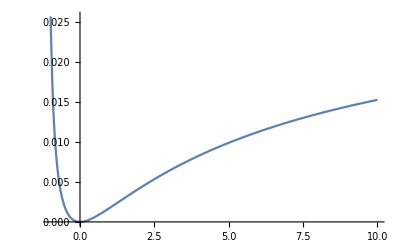

```mathematica
Plot[pfinal[A[lp[k]], B[lm,lp[k],Np]], {k,-0.99,10}]
```